```mathematica
data=Import["/home/artem/projects/solver/tab_func/rcf_H.dat", "table"];
DenN=data[[1,-1]]
TemN=data[[2,-1]]
(*data=data[[5;;Length[data]-1]];*)
```

93

353

```mathematica
ρ=1;
(*ρ=const*)
p=Exp@Table[{data[[TemN*(ρ-1)+ i,2]],data[[TemN*(ρ-1)+i,3]]}, {i,1,TemN}];
ρ=45;
p2=Exp@Table[{data[[TemN*(ρ-1)+ i,2]],data[[TemN*(ρ-1)+i,3]]}, {i,1,TemN}];
ρ=92;
p1=Exp@Table[{data[[TemN*(ρ-1)+ i,2]],data[[TemN*(ρ-1)+i,3]]}, {i,1,TemN}];

(*T=const*)
T=1;
pT=Exp@Table[{data[[i*TemN+T,1]],data[[i*TemN+T,3]]}, {i,0,DenN-1}];
T=352;
pT1=Exp@Table[{data[[i*TemN+T,1]],data[[i*TemN+T,3]]}, {i,0,DenN-1}];
```

```mathematica
lp0=ListLogLogPlot[p,PlotLabel->Style["ρ=const",Black,15], AxesLabel->{"T","λ"},
PlotRange->{{800, 10^6},{10^-50,10^12}}];
lp2=ListLogLogPlot[p2,PlotLabel->Style["ρ=const",Black,15], AxesLabel->{"T","λ"}];
lp1=ListLogLogPlot[p1,PlotLabel->Style["ρ=const",Black,15], AxesLabel->{"T","λ"}];

lT0=ListLogLogPlot[pT, PlotLabel->Style["T=const",Black,15],AxesLabel->{"ρ","λ"},
PlotRange->{{10^-17, 10^-7},{10^-50,10^12}}];
lT1=ListLogLogPlot[pT1, PlotLabel->Style["T=const",Black,15],AxesLabel->{"ρ","λ"}];
```

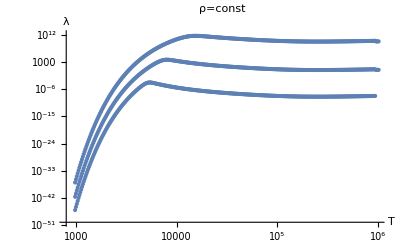

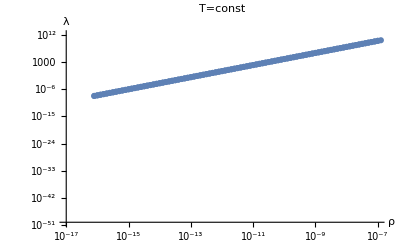

```mathematica
Show[lp0,lp1 ,lp2]
Show[lT0,lT1]
```

```mathematica
σ=5.670374419*10^-5;
σt=6.65210*10^-25;
m=1.6735575*10^-24;
Kb=1.3807*10^-16;
c=3.0*10^10;
h=6.62*10^-27;
(*α=λ/(4 σ T^4)*)
(*β=σt/m ρ*)
```

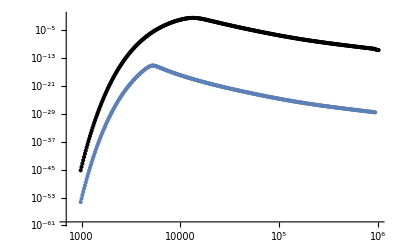

```mathematica
Al=Table[{p[[i,1]],p[[i,2]]/(4 σ (p[[i,1]])^4)},{i,1,Length[p]}];
Al1=Table[{p1[[i,1]],p1[[i,2]]/(4 σ (p1[[i,1]])^4)},{i,1,Length[p]}];
Show[ListLogLogPlot[Al,PlotRange->{{7*10^2, 10^6},{10^-60,10^-1}}],ListLogLogPlot[Al1, PlotStyle->Black]]
```

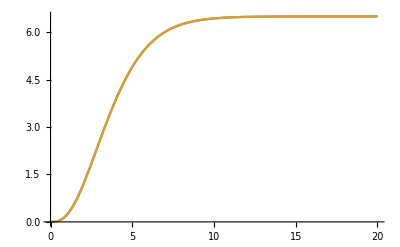

```mathematica
f[x_]:=NIntegrate[t^3/(Exp[t]-1),{t,0,x}]
f0[x_]:=If[x≤2, 
x^3(1/3-x/8+x^2/62.4),If[x<10^6,6.4939-Exp[-x](x^3+3 x^2+6x+7.28),6.4939]]
Plot[{f[x],f0[x]},{x,0,20}, PlotRange->All]

Sk[w_,v_, tem_]:=2 Kb^4 Pi/(c^2 h^3)(f0[(h w)/(Kb tem)]-f0[(h v)/(Kb tem)])1/Pi//N
```

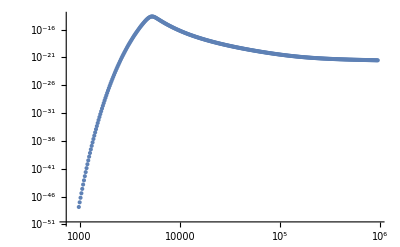

```mathematica
(*w1=10^50; w0=10^-1;*) (*по всему спектру стремится к серой материи*)
w1=c/(600*10^-7);
w0=c/(700*10^-7);

A=Table[{p[[i,1]],p[[i,2]]/(4 Sk[w1,w0,p[[i,1]]] (p[[i,1]])^4)},{i,1,Length[p]}];
ListLogLogPlot[A]
```

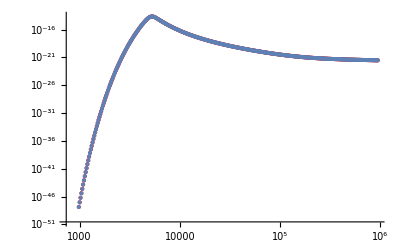

```mathematica
B=2 Kb^4 Pi/(Pi c^2 h^3);
a=h/Kb;

LgF[w_,v_,T_]:= Log[B a^3/(T)^3]-a/(2T)(v+w)+Log[Abs[v^3-w^3]/2 + 3/2 Abs[(v^2-w^2)]+6/2 Abs[(v-w)]]
Sk2[w_,v_, tem_]:=If[(a w)/tem>5*10^2&& (a v)/tem>5*10^2,LgF[w,v,tem],
Log[ B(f0[(h w)/(Kb tem)]-f0[(h v)/(Kb tem)])]//N]


LgAl=Table[{Log@p[[i,1]],Log[p[[i,2]]]-4Log[√2 p[[i,1]]] - Sk2[w1,w0,p[[i,1]]]},{i,1,Length[p]}];

Show[ListLogLogPlot[Exp@LgAl, PlotStyle->Red],
ListLogLogPlot[A]]
```

```mathematica
Max[Table[A[[i,2]]-Exp@LgAl[[i,2]],{i,200,Length[A]}]]
```

2.88889×10^-34

```mathematica
(a w0)/p[[1,1]]
LgF[w1,w0,p[[1,1]]]
```

20548.6 ⅇ^-of

99.8502-22261. ⅇ^-of+Log[3.06822×10^-37 ⅇ^(-3 of)]

```mathematica
h/Kb*(c/(100*10^-7))/1000
```

143.84

```mathematica
(6.62607015*10^-34/(1.380649*10^-23)*3*10^10)1/(100*10^-11 1000)*1/10^4
```

143.977

```mathematica
t=2700.2831;
σ/Pi t^4

ii=i[s]/.DSolve[{D[i[s],s]+α i[s]==Q, i[0]==0},i[s],s][[1]]
ii/.{s->0.3, Q->10,α->10}
```

9.59619×10^8

(ⅇ^(-s α) (-1+ⅇ^(s α)) Q)/α

0.950213

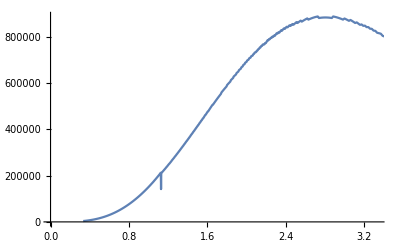

```mathematica
sp=Table[{c/i,ii/.{s->0.3, Q->Sk[c/i,c/(i+(50*10^-8)),t] t^4,α->10^-6/(4 Sk[c/i,c/(i+(50*10^-8)),t] t^4)}},{i,(400.*10^-7),(900.*10^-6),( 50.*10^-8)}];
ListLinePlot[sp]
```

```mathematica
Solve[{y1==k x1+M,y0==k x0+M},{k,M}]//FullSimplify
```

{{k→(y0-y1)/(x0-x1),M→(-x1 y0+x0 y1)/(x0-x1)}}